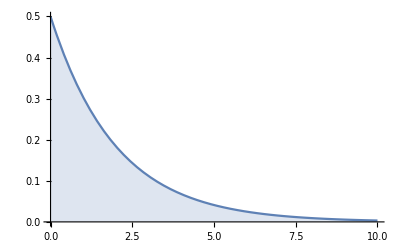

```mathematica
Clear["Global`*"];
Plot[Table[PDF[ChiSquareDistribution[ν],x],{ν,{2}}]//Evaluate,{x,0,10},Filling->Axis]
```

```mathematica
43/15.
```

2.86667

```mathematica
Quantile[ChiSquareDistribution[2],0.95]
```

5.99146

```mathematica
NProbability[z≥28.387, z\[Distributed]ChiSquareDistribution[2]]
```

6.85238×10^-7

```mathematica
For[i=0,i<20,i++,Print[i,"  ",Probability[x<i, x\[Distributed]PoissonDistribution[2.44]]]]
```

0  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

1  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

2  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

3  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

4  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

5  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

6  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

7  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

8  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

9  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

10  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

11  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

12  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

13  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

14  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

15  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

16  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

17  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

18  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

19  Probability[False,19\[Distributed]PoissonDistribution[2.44]]

```mathematica
For[i=0,i<20,i++,Print[i,"  ",Probability[t==i, t\[Distributed]PoissonDistribution[2.44]],"  ",400*Probability[t==i, t\[Distributed]PoissonDistribution[2.44]]]]
```

0  0.0871609  34.8643

1  0.212672  85.069

2  0.25946  103.784

3  0.211028  84.4111

4  0.128727  51.4908

5  0.0628188  25.1275

6  0.0255463  10.2185

7  0.00890471  3.56188

8  0.00271594  1.08637

9  0.00073632  0.294528

10  0.000179662  0.0718649

11  0.0000398523  0.0159409

12  8.10331×10^-6  0.00324132

13  1.52093×10^-6  0.000608372

14  2.65076×10^-7  0.00010603

15  4.31191×10^-8  0.0000172476

16  6.57566×10^-9  2.63026×10^-6

17  9.438×10^-10  3.7752×10^-7

18  1.27937×10^-10  5.11749×10^-8

19  1.64298×10^-11  6.57194×10^-9

```mathematica
Quantile[ChiSquareDistribution[2],0.95]
```

5.99146

```mathematica
NProbability[z≥6.1798, z\[Distributed]ChiSquareDistribution[2]]
```

0.0455065